```mathematica
Clear["Global`*"]
```

```mathematica
(* Automated extraction of parameters from lineage data *)
```

```mathematica
files=FileNames["*.txt","/home/s1402978/Desktop/volume-dep transcription/Analysis_MC4100_37C/MC4100_37C"];
```

```mathematica
data1=Import[#,"CSV",Delimiters->","]&/@files;
```

```mathematica
Length[data1]
```

160

```mathematica
(* Initialize arrays *)
```

```mathematica
data2=Table[0,{i,1,Length[data1]}];
```

```mathematica
data2a=Table[0,{i,1,Length[data1]}];
```

```mathematica
data3a=Table[0,{i,1,Length[data1]}];
```

```mathematica
data3b=Table[0,{i,1,Length[data1]}];
```

```mathematica
CycleLength=Table[0,{i,1,Length[data1]}];
```

```mathematica
Lengthincrement=Table[0,{i,1,Length[data1]}];
```

```mathematica
LengthMap=Table[0,{i,1,Length[data1]}];
```

```mathematica
BirthLength=Table[0,{i,1,Length[data1]}];
```

```mathematica
BirthLengthCycleData=Table[0,{i,1,Length[data1]}];
```

```mathematica
DivisionLength=Table[0,{i,1,Length[data1]}];
```

```mathematica
TAcmeans=Table[0,{i,1,Length[data1]}];
TAcvars=Table[0,{i,1,Length[data1]}];
Weighting = Table[0,{i,1,Length[data1]}];
```

```mathematica
(* Format of data is data1[[lineage number]]{timepoint,divisionindicator,length,per-cell total fluorescence intensity,average fluorescence intensity of the mother cell}. 
Extract the first and second moments of protein fluctuations just before and just after cell division; data2a has the ratios of mean before / mean after; data3 has points {z,2*z1} where z is the FF before division and z1 is the FF after division *)
```

```mathematica
data1[[1]]
```

{{1,1,2.09708,338326,5546.33},{2,0,2.10993,344303,5553.27},{3,0,2.29029,370118,5442.91},{4,0,2.47987,405355,5629.93},{5,0,2.39596,381219,5689.84},{6,0,2.46906,387991,5542.73},{7,0,2.49225,415390,5690.27},{8,0,2.49002,414404,5676.77},{9,0,2.54599,435754,5733.61},2156,{2166,0,3.09336,428029,5631.96},{2167,0,3.06065,423644,5362.58},{2168,0,3.1462,432763,5620.3},{2169,0,3.38488,457192,5442.76},{2170,0,3.39666,471032,5477.12},{2171,0,3.50954,466333,5360.15},{2172,0,3.62553,490543,5390.58},{2173,0,3.75956,517898,5509.55},{2174,0,3.92931,511631,5501.41}}
 |  |  |  |

```mathematica
For[k=1,k≤Length[data1],k++,
(* take in the data into individual arrays *)
DivisionIndicator=Table[data1[[k]][[i]][[2]],{i,1,Length[data1[[k]]]}];FluorescenseData=Table[data1[[k]][[i]][[4]],{i,1,Length[data1[[k]]]}];LengthData=Table[data1[[k]][[i]][[3]],{i,1,Length[data1[[k]]]}];AppVolData=Table[LengthData[[i]](*Pi*0.5^2*),{i,1,Length[data1[[k]]]}](* assume cyclinder units μm^3 *);Concs= Table[FluorescenseData[[i]]/AppVolData[[i]],{i,1,Length[data1[[k]]]}](* prop to conc *);DivisionTimes=DeleteCases[Table[If[DivisionIndicator[[i]]==1,i,0],{i,1,Length[DivisionIndicator]}],0];
(* begin manipulation of the data *)
CycleLength[[k]]=Table[DivisionTimes[[i+1]]-DivisionTimes[[i]],{i,1,Length[DivisionTimes]-1}];TAcmeans[[k]]=Table[Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]]/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}] (* time-avg means over each generation *);
TAcvars[[k]]=Table[(Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]^2]-(TAcmeans[[k]][[i]])^2)/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}](* time-avg variances over each generation *);
(*Weighting=Table[,{i,1,Length[DivisionTimes]-1}];*)
Lengthincrement[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]]-LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];LengthMap[[k]]=Table[{LengthData[[DivisionTimes[[i]]]],LengthData[[DivisionTimes[[i+1]]-1]]},{i,1,Length[DivisionTimes]-1}];BirthLength[[k]]=Table[LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];DivisionLength[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]],{i,1,Length[DivisionTimes]-1}];BirthLengthCycleData[[k]]=Table[Table[LengthData[[i]],{i,DivisionTimes[[j]],DivisionTimes[[j+1]]-1}],{j,1,Length[DivisionTimes]-1}];Fluoafterdiv=Table[FluorescenseData[[DivisionTimes[[i]]]],{i,2,Length[DivisionTimes]}];Fluobeforediv=Table[FluorescenseData[[DivisionTimes[[i]]-1]],{i,2,Length[DivisionTimes]}]; z=N[Variance[Fluobeforediv]/Mean[Fluobeforediv]]; z1=N[Variance[Fluoafterdiv]/Mean[Fluoafterdiv]];y=N[Variance[Fluoafterdiv]-(Variance[Fluobeforediv]/4)];x=N[Mean[Fluobeforediv]];If[y≥0,data2[[k]]={z,2*z1},data2[[k]]=0;];
data2a[[k]]=N[Mean[Fluobeforediv]]/N[Mean[Fluoafterdiv]];];data3=DeleteCases[data2,0];
```

```mathematica
CVmeans = Table[Variance[TAcmeans[[i]]]/Mean[TAcmeans[[i]]],{i,1,Length[TAcmeans]}]; (* coefficient of variation for each lineage of the distribution of time averaged means in each cc generation *)
```

```mathematica
CVvars = Table[Variance[TAcvars[[i]]]/Mean[TAcvars[[i]]],{i,1,Length[TAcvars]}]; (* coefficient of variation for each lineage of the distribution of time averaged variances in each cc generation *)
```

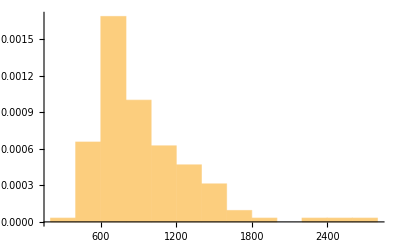

```mathematica
Histogram[CVmeans,Automatic,"PDF"]
```

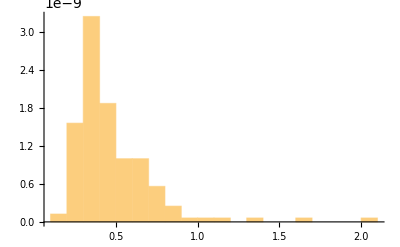

```mathematica
Histogram[CVvars,Automatic,"PDF"]
```

```mathematica
Mean[TAcmeans];
```

```mathematica
mnMns=ListPlot[{Mean[TAcmeans],TAcmeans[[1]],TAcmeans[[100]],TAcmeans[[50]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True,PlotLegends->{"Mean over lineages","Lineage 1","Lineage 2","Lineage 3"}];
mnVars=ListPlot[{Mean[TAcvars],TAcvars[[1]],TAcvars[[100]],TAcvars[[50]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True,PlotLegends->{"Mean over lineages","Lineage 1","Lineage 2","Lineage 3"}];
```

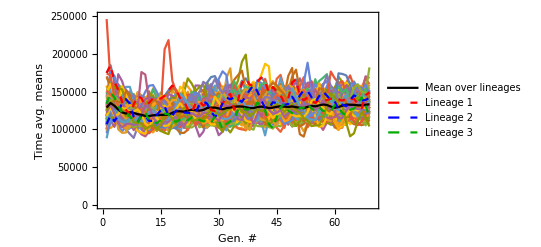

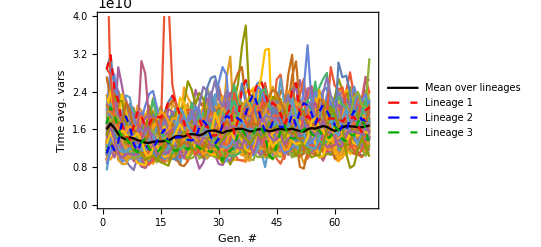

```mathematica
Show[ListPlot[AppendTo[TAcmeans,Mean[TAcmeans]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{Style["Gen. #",12,Bold],Style["Time avg. means",12,Bold]},PlotRange->{{0,70},{0,250000}}],mnMns]
Show[ListPlot[AppendTo[TAcvars,Mean[TAcvars]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{Style["Gen. #",12,Bold],Style["Time avg. vars",12,Bold]},PlotRange->{{0,70},{0,4*10^10}}],mnVars]
```

```mathematica
Dimensions[BirthLengthCycleData]
```

{160,69}

```mathematica
(* Fraction of lineages that are consistent with binomial partitioning with p = 1/2, i.e. they obey the relation 4*Var_after > V_before, i.e. y > 0. This is since binomial partitioning with p = 1/2 implies 4*var_after = var_before + <n>_before  *)
```

```mathematica
N[Length[data3]/Length[data1]]
```

0.5875

```mathematica
(* Using data for those lineages obeying y > 0; Linear plot with slope 1 verifies binomial partitioning with p = 1/2; the intercept is the factor g where fluorescence = g * protein number *)
```

```mathematica
lm=LinearModelFit[data3,x1,x1]
```

FittedModel[269.226+1.1759 x1]

```mathematica
lm["RSquared"]
```

0.942315

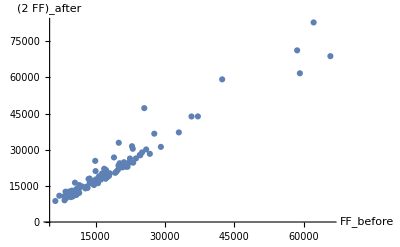

```mathematica
ListPlot[data3,PlotRange->All,AxesLabel->{Subscript[FF,before],Subscript[2*FF,after]}]
```

```mathematica
(* Ratio of protein before and after cell division for ALL lineages; a value of 2 is indication of binomial partitioning with probability of 1/2; note that the mean is greater than 2 on average showing the mother cell has more molecules after partitioning than daughter cells *)
```

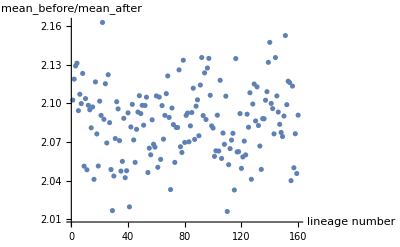

```mathematica
ListPlot[data2a,AxesLabel->{"lineage number",Subscript[mean,before]/Subscript[mean,after]}]
```

```mathematica
(* Fitting Erlang distribution of cell cycle length times; data from all lineages is pooled together *)
```

```mathematica
paramserlang=FindDistributionParameters[Flatten[CycleLength],GammaDistribution[α,β]]
```

{α→29.9381,β→1.08907}

```mathematica
N[Mean[Flatten[CycleLength]]]
```

32.6046

```mathematica
N[Variance[Flatten[CycleLength]]/Mean[Flatten[CycleLength]]^2]
```

0.0352549

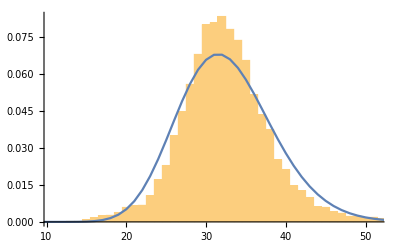

```mathematica
Show[Histogram[Flatten[CycleLength],{1},"PDF"],ListPlot[Table[{x,PDF[GammaDistribution[α,β]/.paramserlang,x]},{x,1,140}],Joined->True,PlotRange->All]]
```

```mathematica
Variance[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

96.9678

```mathematica
Mean[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

53.4455

```mathematica
(* Autocorrelation of cell cycles lengths; there are more negative correlated successive cell cycle lengths than expected by chance; correlation is 7 standard deviations away from mean and hence there is probability of 1 in 390682215445 that it can be explained by chance! however the correlation is weak *)
```

```mathematica
N[CorrelationFunction[Flatten[CycleLength],1]]
```

-0.144847

```mathematica
data4=Table[0,{i,5000}];
```

```mathematica
(*For[k=1,k≤5000,k++,rnddata=Table[RandomVariate[ErlangDistribution[α,β]/.paramserlang,Length[CycleLength[[i]]]],{i,Length[CycleLength]}];data4[[k]]=N[CorrelationFunction[Flatten[rnddata],1]];]*)
For[k=1,k≤5000,k++,rnddata=Table[RandomVariate[GammaDistribution[α,β]/.paramserlang,Length[CycleLength[[i]]]],{i,Length[CycleLength]}];data4[[k]]=N[CorrelationFunction[Flatten[rnddata],1]];]
```

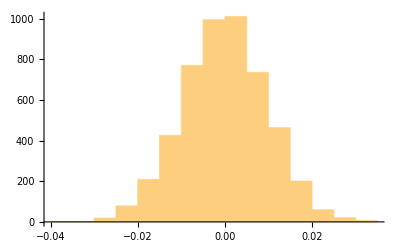

```mathematica
Histogram[data4]
```

```mathematica
7*StandardDeviation[data4]
```

0.0671897

```mathematica
Flatten[Lengthincrement];
```

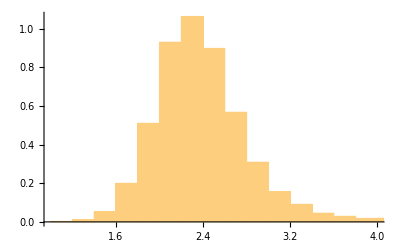

```mathematica
(* Find distribution of length increment from birth to division; does not support an adder where a constant volume is added in each cell cycle *)
Show[Histogram[Flatten[Lengthincrement],Automatic,"PDF"]]
```

```mathematica
StandardDeviation[Flatten[Lengthincrement]]/Mean[Flatten[Lengthincrement]]
```

0.256991

```mathematica
(* Find relationship between final and initial lengths *)
```

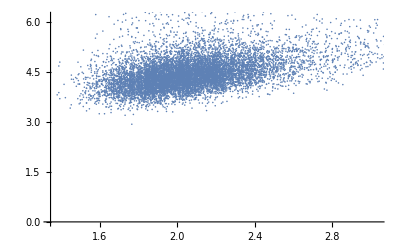

```mathematica
ListPlot[Flatten[LengthMap,1]]
```

```mathematica
lm1=LinearModelFit[Flatten[LengthMap,1],x1,x1]
```

FittedModel[2.57968+0.93241 x1]

```mathematica
lm1["RSquared"]
```

0.244997

```mathematica
(* Calculating the birth length distribution *)
```

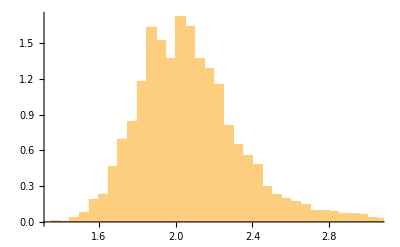

```mathematica
plbl=Histogram[Flatten[BirthLength],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[BirthLength]]
```

2.11073

```mathematica
Variance[Flatten[BirthLength]]/Mean[Flatten[BirthLength]]
```

0.0692436

```mathematica
parambl=FindDistributionParameters[Flatten[BirthLength],GammaDistribution[a,b]]
```

{a→38.9526,b→0.0541873}

```mathematica
paramln=FindDistributionParameters[Flatten[BirthLength],LogNormalDistribution[a,b]]
```

{a→0.734144,b→0.153404}

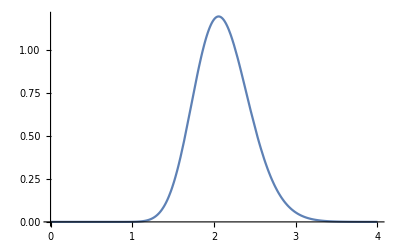

```mathematica
plgammabl=Plot[PDF[GammaDistribution[a,b]/.parambl,h],{h,0,4}]
```

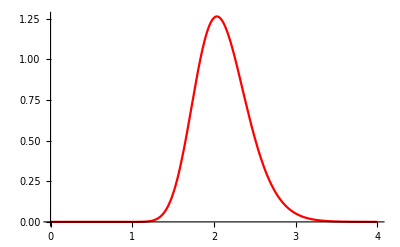

```mathematica
pllnbl=Plot[PDF[LogNormalDistribution[a,b]/.paramln,h],{h,0,4},PlotStyle->Red]
```

```mathematica
bestfitbl=PDF[FindDistribution[Flatten[BirthLength]],h]
```

Piecewise[{{0.+0.125858/(1+11.7878 (-2.61096+h)^2), h≤0}, {0.125858/(1+11.7878 (-2.61096+h)^2)+1.89887×10^12 ⅇ^(-45.1451 h) h^90.2182, True}}]

General::munfl: 0.0000817143^90.2182 is too small to represent as a normalized machine number; precision may be lost.

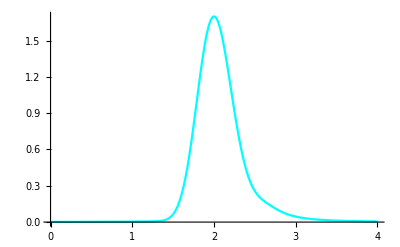

```mathematica
plmixed=Plot[bestfitbl,{h,0,4},PlotStyle->Cyan,PlotRange->All]
```

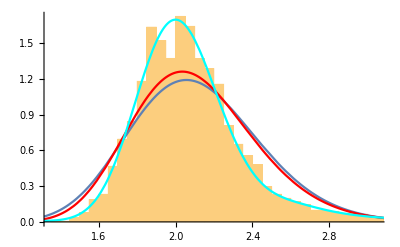

```mathematica
Show[plbl,plgammabl,pllnbl,plmixed]
```

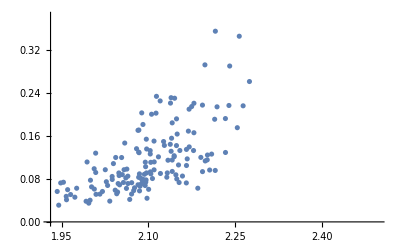

```mathematica
ListPlot[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}]]
```

```mathematica
LinearModelFit[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}],h,h]
```

FittedModel[-2.57896+1.28833 h]

```mathematica
(* The length grows exponential with cellular time; fit length vs cellular time to exponential fn and report Rsquared of plot. Mean Rsquared (calculated across cell cycles and lineages) is very close 1.  *)
```

```mathematica
datA1=Table[Table[Table[{i,BirthLengthCycleData[[w]][[j]][[i]]},{i,1,Length[BirthLengthCycleData[[w]][[j]]]}],{j,1,Length[BirthLengthCycleData[[w]]]}],{w,1,Length[BirthLengthCycleData]}];
```

```mathematica
Dimensions[datA1][[1]]
```

160

```mathematica
datA2=Table[Table[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]["RSquared"],{i,1,Dimensions[datA1][[2]]}],{w,1,Dimensions[datA1][[1]]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Mean[Flatten[datA2]]
```

0.998986

```mathematica
Variance[Flatten[datA2]]
```

1.5279×10^-7

```mathematica
(* The growth rate is extracted by fitting exponential fn to length vs time curves for each cell cycle in each lineage *)
```

```mathematica
datA3=Table[Table[Coefficient[FullSimplify[Log[Normal[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]]],Assumptions->h>0],h],{i,1,Dimensions[datA1][[2]]}],{w,1,Dimensions[datA1][[1]]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

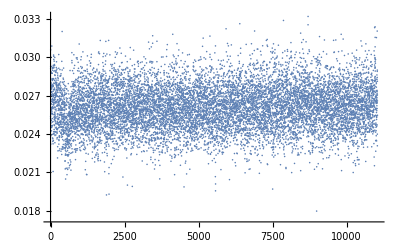

```mathematica
ListPlot[Flatten[datA3]]
```

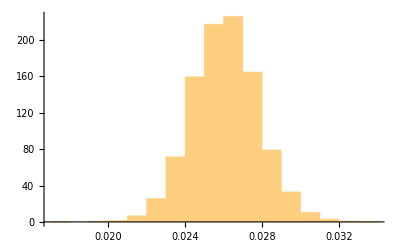

```mathematica
Histogram[Flatten[datA3],Automatic,"PDF"]
```

```mathematica
Dimensions[datA3]
```

{160,69}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1402978/Desktop/Tanouchi-Inference-Project/Julia_analysis

```mathematica
datA3
```

{{0.0253772,0.0252313,0.0290981,0.0292636,0.030578,0.0251069,0.0238617,0.0232116,0.0248491,0.0276009,0.0259921,0.0264058,0.0239065,43,0.0287459,0.0260589,0.026676,0.0252102,0.0281859,0.0291756,0.0256102,0.0277328,0.0261383,0.028989,0.0236928,0.0267843,0.0271295},158,{1}}
 |  |  |  |

```mathematica
Export["exp_grs_all.csv",datA3,"CSV"]
```

exp_grs_all.csv

```mathematica
a = Import["exp_grs_all.csv"]
```

{{0.0253772,0.0252313,0.0290981,0.0292636,0.030578,0.0251069,0.0238617,0.0232116,0.0248491,0.0276009,0.0259921,0.0264058,0.0239065,43,0.0287459,0.0260589,0.026676,0.0252102,0.0281859,0.0291756,0.0256102,0.0277328,0.0261383,0.028989,0.0236928,0.0267843,0.0271295},158,{1}}
 |  |  |  |

```mathematica
Dimensions[a]
```

{160,69}

```mathematica
(* Calculating ratio of birth length at generation i to division length at generation i - 1 *)
```

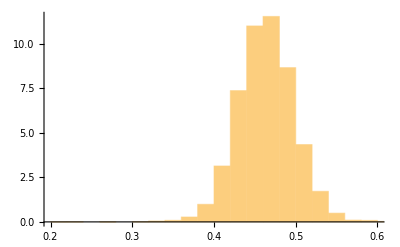

```mathematica
plratio1=Histogram[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.463705

```mathematica
StandardDeviation[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.0347491

```mathematica
paramsratio=FindDistributionParameters[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],BetaDistribution[μ,σ]]
```

{μ→94.5454,σ→109.345}

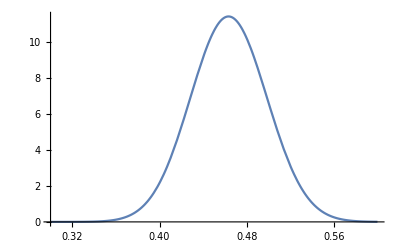

```mathematica
plratio2=Plot[PDF[BetaDistribution[μ,σ]/.paramsratio,h],{h,0.30,0.60}]
```

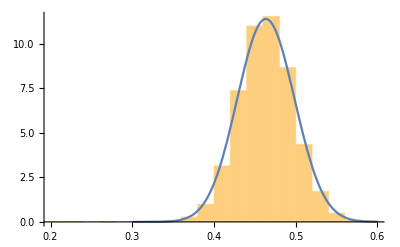

```mathematica
Show[{plratio1,plratio2}]
```

```mathematica
(* Calculating theta *)
```

```mathematica
DivisionLength[[20]]
```

{4.67449,4.35506,4.07558,4.18785,4.14175,4.06071,4.15001,4.32022,4.2648,4.18804,4.36488,3.9735,3.93618,3.73937,3.57469,3.73441,3.88169,3.80703,4.34224,3.86614,4.53638,4.65552,4.60783,7.03246,6.13612,4.4969,4.24629,5.16709,4.71481,3.9831,3.70063,4.13533,3.98284,3.8548,3.81759,3.62271,4.15825,4.18269,4.03363,4.38878,4.13565,4.81612,4.88842,7.54571,6.23449,5.57102,5.6127,5.51366,4.80878,4.59658,5.22897,4.47609,4.43575,4.02431,4.9064,4.46882,4.60404,5.79849,4.35062,4.19867,4.14709,4.85474,4.06414,4.01613,4.35627,4.20247,4.23201,4.74585,3.84397}

```mathematica
BirthLength[[20]]
```

{1.99556,2.34209,1.95527,1.92304,1.81456,1.95751,1.81513,1.85796,2.02802,2.03502,1.88032,1.95644,1.77505,1.83926,1.59541,1.42371,2.01277,1.74866,1.65287,2.08268,1.82382,1.9728,1.96305,2.13891,3.79341,2.81651,1.91374,2.05636,2.40396,2.57521,1.93299,1.41689,1.8755,1.99087,1.76652,1.71128,1.70916,1.7728,1.69971,1.56243,1.93219,1.91374,2.28052,2.41957,3.38748,3.20851,2.66301,2.58002,2.69023,2.40451,2.16477,2.2358,2.13331,1.91873,1.92478,2.17432,2.22974,2.2146,2.45257,1.91773,2.21489,1.94937,2.19249,2.01913,2.0713,1.75478,1.92461,1.99069,2.09603}

```mathematica
CycleLength[[20]]
```

{37,28,28,30,29,33,38,34,30,30,41,30,32,31,32,36,31,34,40,26,34,37,34,54,20,21,37,43,27,19,27,48,31,28,30,29,34,34,31,42,32,35,30,51,23,23,32,32,25,31,33,26,35,35,39,30,33,38,21,30,30,43,26,32,35,38,29,34,28}

```mathematica
Lambda=(DivisionLength[[20]]/BirthLength[[20]])
```

{2.34245,1.85948,2.08441,2.17772,2.28251,2.07443,2.28634,2.32525,2.10294,2.05798,2.32135,2.03098,2.2175,2.03308,2.24061,2.62301,1.92853,2.17711,2.62709,1.85633,2.4873,2.35985,2.34728,3.28787,1.61757,1.59662,2.21884,2.51274,1.96127,1.54671,1.91446,2.9186,2.12362,1.93624,2.16108,2.11696,2.43292,2.35937,2.37313,2.80895,2.1404,2.5166,2.14355,3.11862,1.84045,1.73633,2.10765,2.13706,1.7875,1.91165,2.41549,2.00201,2.07928,2.09738,2.54907,2.05527,2.06483,2.6183,1.7739,2.1894,1.87237,2.49041,1.85366,1.98904,2.10316,2.39487,2.19889,2.38402,1.83393}

```mathematica
Mean[Lambda/BirthLength[[20]]]
```

1.10051

```mathematica
Theta=1/(BirthLength[[20]]*(1 + BirthLength[[20]]/Lambda)*Log[1+Lambda/BirthLength[[20]]])
```

{0.348481,0.323337,0.363672,0.364671,0.376977,0.363746,0.376735,0.368622,0.352825,0.353586,0.365434,0.365642,0.386007,0.383421,0.417314,0.435821,0.361763,0.392153,0.390319,0.355074,0.367726,0.350933,0.352708,0.304234,0.221885,0.286032,0.364435,0.334972,0.313295,0.309771,0.373972,0.42483,0.373926,0.364553,0.389824,0.401336,0.388228,0.380595,0.39228,0.399741,0.364799,0.353603,0.320619,0.281051,0.239496,0.253019,0.28455,0.291018,0.291248,0.314857,0.325062,0.330436,0.340051,0.368484,0.350967,0.33587,0.328973,0.313482,0.314447,0.364991,0.337582,0.349593,0.341022,0.358442,0.34708,0.382125,0.363623,0.347684,0.354188}

```mathematica
Mean[Theta]
```

0.349119

```mathematica
Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.00259813

```mathematica
Mean[Theta]+Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.351718

```mathematica
Mean[Theta*CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.35168

```mathematica
0.72/Mean[BirthLength[[20]]]
```

0.345849

```mathematica
1/Mean[Flatten[BirthLengthCycleData[[20]]]]
```

0.335766